# Fit vertex angles in experiments, measure domain sizes, and the number of vertices (corners) of each domain

[MinD] = 1.5 µM
[MinE-His] = 3 µM

```mathematica
img=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180420_ch9_1.5uM-D_3uM-E-His_40x_01_hex-pattern.lsm"];
```

```mathematica
img2=First@First@First@Import[ParentDirectory@ParentDirectory@ParentDirectory[NotebookDirectory[]]<>"/GlockEtAl-RawData/Glock et al. MinE-His Stationary patterns-snapshots/180420_ch9_1.5uM-D_3uM-E-His_40x_03.lsm"];
```

Separate MinD and MinE channels

```mathematica
imgSep=ColorSeparate[img];
imgSep2=ColorSeparate[img2];
```

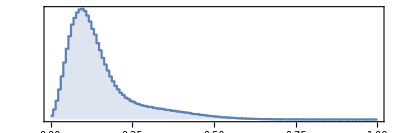
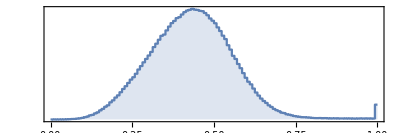

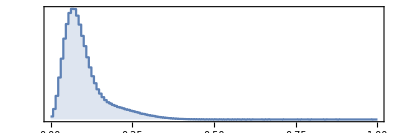
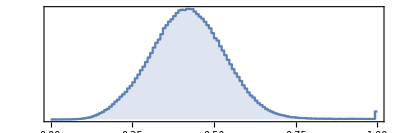

```mathematica
ImageHistogram/@ImageAdjust/@imgSep
ImageHistogram/@ImageAdjust/@imgSep2
```

```mathematica
imgReg={ImageAdjust[ImageAdjust@imgSep[[1]],0,{0,0.6}],ImageAdjust@imgSep[[2]]};
imgReg2={ImageAdjust[ImageAdjust@imgSep2[[1]],0,{0,0.4}],ImageAdjust@imgSep2[[2]]};
```

```mathematica
colorMap={minD,minE,minE+minD/1.5};
```

Image 1, Main text Fig. 4a

```mathematica
imgColor=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg))
```

Image 2, Extended Data Fig. 1

```mathematica
imgColor2=ColorCombine[Image/@#,"RGB"]&@((colorMap/.{minD->#[[2]],minE->#[[1]]})&@(ImageData/@ImageAdjust/@imgReg2))
```

## Image preparation

### MinD-MinE pixel clustering (using first image)

```mathematica
classImage=BrightnessEqualize[ImageAdjust[#]]&/@imgSep;
```

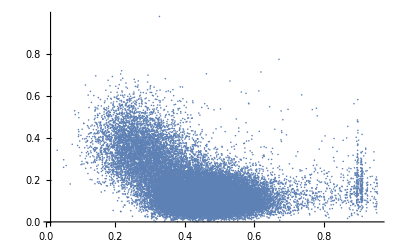

```mathematica
ListPlot[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}[[All,;;200,;;200]]],PlotRange->All]
```

```mathematica
clusters=FindClusters[Transpose[Flatten/@{ImageData[classImage[[2]]],ImageData[classImage[[1]]]}],2,Method->"KMeans",DistanceFunction->EuclideanDistance];
```

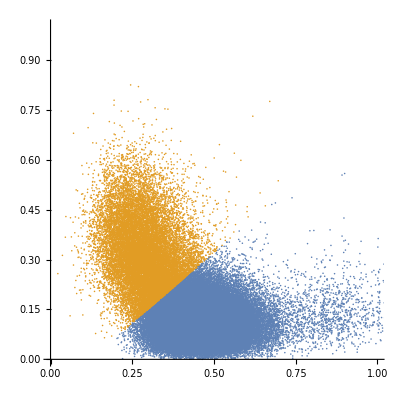

```mathematica
ListPlot[clusters[[All,;;;;10]],PlotRange->{{0,1},{0,1}},AspectRatio->1]
```

```mathematica
centroids=Mean/@clusters;
```

```mathematica
ratioDE=#[[1]]/#[[2]]&@First@Differences[centroids]
```

-0.846452

### Image binarization

```mathematica
ClearAll@meshBinarize;
Options[meshBinarize]={"ThresholdPixelNumber"->10};
meshBinarize[img_,ratioDE_,opts:OptionsPattern[]]:=Block[
{imgEq=BrightnessEqualize[ImageAdjust[#]]&/@img,
minDMeas,
minE,
minD,
imgProj,
imgBinarized,
morphImg,
smallComponents,
morphMask,
imgBinarizedCleaned
},
minDMeas=ImageMeasurements[imgEq[[2]],{"Mean","StandardDeviation"}];
minE=imgEq[[1]];
(*to ignore MinD aggregates, cut brightness at mean+std off*)
minD=ImageClip[imgEq[[2]],{0,Total@minDMeas}];
(*project pixel MinD MinE fluorescence values on the axis connecting the centroids of the clusters identified in the initial image*)
imgProj=Image[ImageData[minE]+ratioDE ImageData[minD]];
(*binarize along this axis, and smooth to get a connected mesh*)
imgBinarized=Binarize[GaussianFilter[Binarize[ImageAdjust@imgProj],5],0.3];

(*remove too small morphological components*)
morphImg=MorphologicalComponents[imgBinarized];
smallComponents=Keys@Select[ComponentMeasurements[morphImg,"Area"],#[[2]]<10&];
morphMask=Clip[morphImg/.Thread[smallComponents->-1],{-1,0}];
imgBinarizedCleaned=Image[ImageData[imgBinarized]+morphMask];

{imgProj,imgBinarizedCleaned}
]
```

```mathematica
imgProj=meshBinarize[imgSep,ratioDE];
```

```mathematica
(*Export[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-1.tiff",imgProj[[1]]];
Export[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-2.tiff",imgProj[[2]]];*)
```

```mathematica
(*imgProj={Import[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-1.tiff"],Import[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-2.tiff"]};*)
```

```mathematica
imgProj2=meshBinarize[imgSep2,ratioDE];
```

```mathematica
(*Export[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-exp3-1.tiff",imgProj2[[1]]];
Export[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-exp3-2.tiff",imgProj2[[2]]];*)
```

```mathematica
(*imgProj2={Import[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-exp3-1.tiff"],Import[NotebookDirectory[]<>"img-MinD_1_5-MinEHis_3-exp3-2.tiff"]};*)
```

Skeleton of the network

```mathematica
branchIm=Thinning[imgProj[[2]]]
```

-Graphics-

```mathematica
branchIm2=Thinning[imgProj2[[2]]];
```

## Junction Analysis

### Measurement functions

Fit the vertex by assuming Gaussian cross-sections of the vertex arms:

```mathematica
ClearAll@lossF;
lossF[vertexData_,x1_?NumericQ,x2_?NumericQ,angles_?VectorQ]:=
Total[
Function[d,
(d[[3]]-Exp[-#/((width/2)^2/Log[2])])^2&@Min[If[Length@#==0,{1000},#]&@((Norm[d[[{1,2}]]-{x1,x2}]^2-((d[[{1,2}]]-{x1,x2}).{Cos[#],Sin[#]})^2)&/@
Select[angles,
Function[angle,((d[[{1,2}]]-{x1,x2}).{Cos[angle],Sin[angle]})>-10^-10]
])
]]/@vertexData[[2]]];
```

```mathematica
ClearAll@measureData;
measureData[vertexData_,armNumber_]:=
Block[
{
dataW,
iniCond,
iniCondClean,
vars,
sol,sol2,
fitSuccess=1,
fit
},
(*get initial conditions for the angles of the vertex arms by making a radial histogram and finding its peaks*)
dataW=WeightedData[#[[All,1]],#[[All,2]]]&@({PlanarAngle[{0,0}->{{1,0},#[[{1,2}]]}],#[[3]]}&/@Transpose[{vertexData[[2,All,1]],vertexData[[2,All,2]],Rescale@vertexData[[2,All,3]]}]);
iniCond=If[#[[1]]>Pi,{#[[1]]-2Pi,#[[2]]},#]&/@({0.05+(HistogramList[dataW,{0,2Pi,0.2}][[1,#[[1]]]]),#[[2]]}&/@(FindPeaks[Last@HistogramList[dataW,{0,2Pi,0.2}],1,0,0,Padding->"Periodic"]));
(*take mean of peaks that lie close together; map angles onto [-Pi,Pi] range*)
iniCondClean=If[#>Pi,#-2Pi,If[#<-Pi,#+2Pi,#]]&/@
SortBy[DeleteDuplicates@Table[
Mean[
Select[Join[iniCond,{#[[1]]-2Pi,#[[2]]}&/@iniCond,{#[[1]]+2Pi,#[[2]]}&/@iniCond],Min[Abs[#[[1]]-ini[[1]]]<0.5&]]
],{ini,iniCond}],#[[2]]&][[All,1]];
If[Length[iniCondClean]<3,
sol=I,
iniCond=iniCondClean[[-armNumber;;]];
vars=Symbol["a"<>ToString[#]]&/@Range[Length@iniCond];
Quiet@Check[sol=Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2];,fitSuccess=0;];
(*Try a second time if it failed*)
If[fitSuccess==0,
sol2=Check[Last@FindMinimum[lossF[vertexData,x1,x2,vars],Join[{{x1,0,-10,10},{x2,0,-10,10}},{vars[[#]],iniCond[[#]],-2Pi,2Pi}&/@Range[Length@iniCond]],AccuracyGoal->2,PrecisionGoal->2,Method->"PrincipalAxis"],I];
sol=sol2;
];
];
If[sol===I,
I,
fit=Join[{vertexData[[1,1]]+x1,vertexData[[1,2]]+x2}/.sol,Sort[If[#<-Pi,#+2Pi,If[#>Pi,#-2Pi,#]]&/@(vars/.sol)]];
If[Min[Abs@Differences[fit[[2;;]]]]<0.01,
I,
fit]
]
];
```

## Determine branch points

The branch width is about 2 pixels, see below.
We prun branches shorter than 10 pixels because for their vertices no reliable angles can be determined (repeatedly to account for short, branched segments that we want to remove).

```mathematica
branchImPrun=Thinning[Pruning[Pruning[Pruning[branchIm,10],10],10]]
```

-Graphics-

```mathematica
branchPoints=MorphologicalBranchPoints[Binarize@branchImPrun];
```

```mathematica
branchPointCoords=ImageValuePositions[branchPoints,1];
```

```mathematica
HighlightImage[branchImPrun,{AbsolutePointSize[3],branchPointCoords}]
```

-Graphics-

```mathematica
branchImPrun2=Thinning[Pruning[Pruning[Pruning[branchIm2,10],10],10]];
branchPoints2=MorphologicalBranchPoints[Binarize@branchImPrun2];
branchPointCoords2=ImageValuePositions[branchPoints2,1];
```

## Average branch widths (using first image)

Determine average branch width by binarizing the experimental network image (imgProj[[1]]) at half-maximum intensity, count the white pixels (width*length of network) and divide by the white pixels in the network skeleton (length of network because everywhere only one pixel wide)

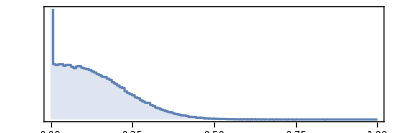

```mathematica
ImageHistogram[imgProj[[1]]]
```

Set 0.25 as branch intensity maximum

```mathematica
width=N@Total@Flatten@ImageData[Binarize[ImageAdjust[imgProj[[1]],0,{0,0.25}],0.5]]/(Total@Flatten@ImageData@branchIm)
```

2.24577

## Vertices - Image 1

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords,0.]]}]/@branchPointCoords,#[[-1]]>10&];
Length@tripleVerticesRaw
```

494

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices=Block[{
tvs=tripleVerticesRaw,
branches=branchImPrun,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices
```

493

### 4-fold vertices

```mathematica
quadrupleVerticesRaw=Complement[branchPointCoords,tripleVertices[[All,1]]];
quadrupleVertices=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw],I];
Length@quadrupleVertices
```

32

```mathematica
vertices=Join[tripleVertices,quadrupleVertices];
```

```mathematica
HighlightImage[branchIm,{AbsolutePointSize[3],tripleVertices,AbsolutePointSize[6],quadrupleVertices}]
```

-Graphics-

## Analysis of triple vertices - Image 1

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

493

```mathematica
failedVertices
```

{}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
Show[
HighlightImage[imgProj[[1]],{AbsolutePointSize[5],tripleVertices}],
Graphics[Join[{Darker@Red,Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{255,150,20}/255]},
Circle[#,3]&/@quadrupleVertices]]
]
```

-Graphics-

```mathematica
angles3=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

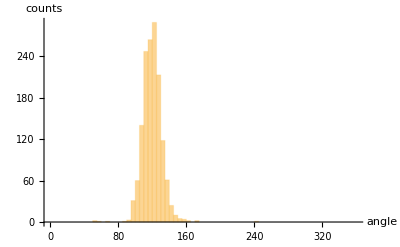

```mathematica
Histogram[{
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles3,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles3,1]]
```

11.4261

#### FitList

```mathematica
vertex3MeasurementsRaw
```

{{951.766,986.555,-2.61713,-0.631261,1.31386},{631.528,985.436,-1.2624,1.12464,3.04412},{558.503,984.496,-1.5542,0.661972,2.72331},{211.742,975.023,-2.72106,-0.556858,1.31263},{875.139,972.672,-2.93135,-0.707544,1.57067},{494.895,971.737,-2.98007,-0.873817,1.10633},{719.251,970.817,-1.78372,0.784798,2.6173},{22.5041,969.501,-1.28317,0.623941,2.81039},{100.517,968.509,-1.51282,0.66032,2.60496},{197.505,968.494,-1.89159,0.41732,2.46884},{459.49,967.501,-2.01872,0.0832561,2.11098},{376.976,964.412,-2.40117,-0.329364,1.74565},{804.912,962.133,-1.83417,0.189778,2.13774},{901.513,952.501,-1.52027,0.629118,2.52393},{450.15,947.49,-2.87554,-0.881357,1.18659},{712.77,949.071,-2.91181,-0.964701,1.16511},{256.022,947.457,-1.54545,0.776624,2.62831},{99.1703,942.995,-2.89107,-0.668471,1.41597},{344.504,940.507,-1.01664,0.706852,2.88067},{425.488,939.516,-1.60287,0.377273,2.33151},{800.495,937.5,-2.43931,-0.614859,1.46937},{513.501,936.499,-2.46743,-0.376115,1.89527},{35.6401,934.967,-1.87325,0.0742324,2.04864},{556.506,932.503,-2.39669,-0.384515,1.41978},{350.515,926.489,-2.27587,-0.438309,1.8106},{546.539,923.52,-1.47545,0.734836,2.59127},{30.6601,920.972,-2.8656,-1.05458,1.20324},{159.504,920.514,-0.917946,0.798651,3.04884},{124.499,918.51,-2.04888,0.18936,2.33087},{487.503,917.512,-1.44306,0.584788,2.67434},{633.507,915.515,-1.65267,0.573736,2.6601},{420.513,914.503,-2.68952,-0.809283,1.20411},{978.563,913.211,-2.84862,-0.596237,1.41714},{899.266,909.057,-2.89873,-0.720977,1.40973},{733.497,906.492,-2.52244,-0.361805,1.76797},{116.495,904.011,-2.75482,-1.13964,1.03031},{393.507,900.51,-1.53933,0.509347,2.51551},{773.507,900.506,-2.86955,-0.919792,1.14687},{834.483,899.493,-2.16278,0.0140027,2.0016},{178.745,897.792,-1.86928,-0.170536,2.31255},{203.138,889.893,-1.23251,0.74261,2.6893},{702.5,886.507,-1.62287,0.509099,2.4357},{441.111,882.625,-2.37794,-0.168672,1.9995},{628.603,883.936,-2.75445,-0.952827,1.36941},{785.504,881.505,-2.15572,-0.137084,2.04702},{823.53,881.626,-3.00766,-1.06319,1.0795},{317.608,879.08,-1.28478,1.00551,2.87861},{406.471,861.531,-2.10117,0.258485,2.17934},{588.502,861.503,-1.46475,0.670402,2.68513},{232.402,854.875,-1.37143,0.93009,2.66212},{324.497,854.495,-2.45636,-0.377112,1.83019},{401.069,852.397,-1.09641,1.04964,3.10668},{538.514,847.501,-2.59144,-0.594471,1.39812},{348.674,845.646,-1.57314,0.481785,2.84088},{660.499,840.492,-2.23569,0.00639478,2.24137},{879.73,838.725,-1.07014,0.936061,3.11545},{763.22,836.64,-3.12902,-1.0008,1.1719},{853.183,838.791,-1.85089,0.0170164,2.21944},{235.52,836.489,-2.48345,-0.535461,1.70536},{302.505,835.5,-1.17834,0.735804,3.0814},{112.498,833.446,-3.00171,-0.922042,1.08445},{412.969,833.184,-2.1943,-0.259566,2.17292},{940.506,833.493,-2.51839,-0.52342,1.67432},{72.495,831.486,-2.07682,-0.0377711,1.97191},{588.929,829.197,-2.73548,-0.449593,1.52926},{495.919,828.375,-1.84823,0.169687,1.96924},{175.498,826.489,-2.54246,-0.606532,1.58823},{251.504,826.527,-1.44516,0.581195,2.57336},{574.007,823.472,-1.84076,0.312307,2.49283},{776.508,811.494,-2.29427,-0.333797,2.00837},{199.494,809.498,-1.6489,0.650069,2.51657},{895.137,809.53,-2.05881,0.273999,2.04771},{129.441,807.379,-1.80353,0.249761,2.04346},{489.602,806.739,-2.87707,-0.790605,1.27976},{630.848,803.865,-1.1845,0.938598,2.81622},{845.47,803.463,-2.53157,-0.559756,1.53311},{463.105,802.406,-1.96769,0.0561307,2.39996},{888.517,798.484,-2.92404,-0.858757,1.01846},{837.383,797.409,-1.62478,0.649481,2.28275},{57.5053,796.506,-2.69383,-0.504449,1.37908},{352.488,792.507,-2.68781,-0.60023,1.63606},{259.476,791.49,-2.25801,-0.202443,1.98105},{637.497,789.523,-2.35659,-0.24647,2.02391},{125.067,787.54,-2.87826,-0.990391,1.37818},{302.52,787.487,-3.10557,-0.77249,1.21307},{696.036,782.51,-2.97345,-0.801313,1.46184},{391.521,780.863,-2.68086,-0.577329,1.43365},{17.4813,779.501,-2.19837,0.0456241,2.15288},{555.869,778.892,-3.12312,-1.09093,1.07435},{312.498,776.509,-1.76157,0.398929,2.23975},{379.479,775.517,-1.70289,0.269415,2.77017},{523.492,775.513,-2.0093,0.195769,2.36399},{197.501,767.497,-2.55292,-0.601869,1.55318},{438.505,763.505,-1.17102,0.788072,2.77383},{912.305,762.827,-1.98915,-0.0841397,2.17786},{943.935,760.36,-0.874627,1.03765,3.08939},{377.634,758.705,-2.64642,-0.953736,1.4571},{717.494,755.479,-2.11919,-0.0753134,2.1553},{738.893,753.774,-1.12421,1.07514,3.05914},{123.515,753.503,-1.09692,0.925837,2.86736},{608.416,748.201,-3.1032,-0.901893,1.02789},{572.244,745.942,-2.10712,0.0904025,2.03945},{514.493,738.5,-2.6743,-0.543937,1.51284},{747.511,735.506,-2.15905,-0.324055,2.01135},{133.697,730.786,-2.36394,-0.210975,1.92993},{840.507,730.503,-2.32624,-0.364773,1.78666},{453.311,730.245,-2.12464,-0.163486,2.03577},{146.628,727.707,-1.41636,0.59807,2.86389},{251.751,725.77,-1.84434,-0.0316964,2.25401},{396.102,722.443,-2.5393,-0.395547,1.91154},{961.494,722.501,-2.25908,-0.121884,1.89183},{50.251,722.201,-1.23955,0.828513,2.99235},{554.562,721.327,-1.4379,0.851958,2.76385},{483.431,720.104,-1.55761,0.641025,2.68067},{887.508,714.497,-1.16857,0.856298,2.91043},{296.187,713.881,-1.72865,0.388365,2.57251},{418.497,709.505,-1.62644,0.402046,2.49332},{636.495,708.493,-2.19522,-0.090426,2.15782},{666.51,702.518,-1.1295,0.74196,2.83604},{800.767,704.039,-1.77863,0.256895,2.41674},{330.055,701.692,-1.72792,-0.0346898,2.1697},{360.076,699.452,-1.20305,0.71163,3.03267},{894.506,696.506,-2.36215,-0.31531,1.8374},{58.5078,693.512,-2.47531,-0.489273,1.79264},{483.61,684.686,-2.65483,-0.40017,1.57334},{923.44,686.486,-1.36875,0.724203,2.79698},{240.51,683.504,-2.88195,-0.780396,1.24735},{553.885,683.074,-2.99171,-0.569664,1.3451},{165.552,683.541,-2.15074,-0.17045,2.22696},{207.013,682.055,-2.45815,-0.330312,1.60211},{537.295,680.248,-2.62553,0.203577,2.65126},{91.6507,677.367,-1.19637,0.894944,2.6984},{199.968,676.246,-1.28624,0.673763,2.83874},{795.501,673.503,-2.40414,-0.55257,1.46355},{516.499,670.502,-1.79734,0.0319782,2.69853},{604.191,672.549,-2.94121,-1.13007,0.816459},{572.5,669.503,-1.74116,-0.000294236,2.49294},{677.507,668.498,-2.2883,-0.210887,1.80965},{926.656,668.998,-2.39918,-0.530312,1.74076},{95.8859,666.224,-1.7807,0.0709606,1.95701},{372.493,662.502,-2.44474,-0.377581,1.92374},{723.251,661.268,-0.98992,1.192,3.09967},{150.812,662.805,-1.18866,0.915043,3.06251},{436.1,662.084,-1.676,0.317421,2.28677},{276.824,657.578,-1.19786,0.962867,2.78206},{855.523,650.488,-2.96168,-0.959248,0.987644},{825.494,646.504,-2.01772,0.100324,2.28916},{436.481,645.492,-2.56033,-0.750538,1.67081},{734.394,646.006,-2.06191,-0.13933,2.21813},{282.047,643.516,-2.16549,-0.138195,1.91865},{758.514,640.516,-1.09207,0.754372,2.82712},{87.5253,637.495,-2.91871,-0.920195,1.21172},{342.503,636.506,-3.05753,-0.986183,0.744926},{405.518,634.478,-2.27219,-0.0551196,2.05628},{24.6766,632.724,-1.87177,0.0641496,2.30345},{418.932,633.019,-1.22438,0.700609,2.96407},{868.472,629.807,-2.01166,-0.0373461,2.07287},{970.496,629.517,-2.0365,0.158028,2.33263},{574.505,628.493,-2.31029,-0.357085,1.84075},{211.721,627.747,-2.19892,-0.338022,1.87477},{499.511,627.493,-3.14126,-0.977618,0.946341},{895.51,627.508,-1.12601,0.910112,3.00898},{620.607,623.909,-2.36428,-0.161664,1.74895},{650.908,623.028,-3.06672,-0.74815,1.34975},{270.013,623.834,-2.85776,-1.03278,1.04336},{814.532,618.283,-2.97574,-0.809345,1.2639},{610.542,613.265,-1.74894,0.826878,2.70298},{167.906,610.787,-2.67514,-0.373962,1.73047},{240.498,611.505,-1.84278,0.492362,2.44708},{663.19,611.935,-1.83397,-0.0700296,2.41934},{778.505,609.501,-1.74947,0.283458,2.22618},{100.358,605.779,-2.39601,-0.395121,1.73892},{703.494,606.505,-1.03628,0.845615,3.01584},{194.327,603.764,-1.12826,0.98997,3.01196},{367.197,603.865,-1.9276,0.467266,2.32821},{853.525,599.143,-2.95753,-0.684631,1.10576},{512.512,598.482,-2.51954,-0.621407,1.80341},{835.503,595.518,-1.98635,0.206894,2.29102},{544.812,595.566,-2.83168,-1.07611,0.884912},{16.7025,592.295,-2.90971,-0.656141,1.47391},{124.583,595.046,-1.54772,0.282605,2.70366},{234.827,591.637,-3.1228,-1.10526,1.29668},{362.697,591.292,-2.74562,-0.872486,1.2126},{200.685,590.011,-2.03792,0.0676456,1.99987},{287.5,589.502,-2.35234,-0.329858,1.96249},{526.447,589.102,-1.49337,0.383975,2.60628},{774.645,582.196,-2.8839,-0.831228,1.46188},{908.685,578.37,-2.59951,-0.292118,1.6942},{938.506,573.491,-0.87933,0.973891,3.1005},{822.507,572.515,-0.985067,0.94736,3.0309},{328.519,571.51,-1.54979,0.544088,2.64614},{426.518,570.512,-2.54483,-0.506683,1.50105},{785.48,570.529,-1.91328,0.173797,2.34218},{893.497,567.498,-2.11921,0.665433,2.35344},{247.443,564.775,-2.28058,-0.0438367,2.00786},{57.5119,564.506,-1.4894,0.705138,2.54209},{262.857,564.016,-1.11047,0.89708,3.0476},{729.925,563.348,-1.90231,0.44219,2.2842},{949.236,560.87,-1.98105,0.111745,2.27192},{127.488,557.495,-2.45268,-0.361924,1.72031},{594.88,557.841,-1.01358,1.09438,3.09449},{381.111,555.128,-2.16023,0.152987,1.92992},{196.877,548.491,-2.06687,-0.104531,1.55468},{724.701,548.626,-2.99919,-1.01503,1.21139},{327.511,543.502,-2.58275,-0.682829,1.48087},{665.491,543.487,-2.19582,-0.0446312,2.13811},{780.502,542.489,-2.51877,-0.486515,1.54209},{826.512,534.491,-2.95365,-0.831048,1.22091},{89.926,532.638,-1.14378,0.675737,2.8504},{363.514,527.479,-2.86535,-0.843195,1.00246},{549.494,525.504,-2.30225,-0.342567,1.60301},{350.5,523.525,-1.855,0.305165,2.36437},{288.492,522.504,-2.03365,0.46647,2.25898},{745.485,518.492,-1.26736,0.605135,2.31556},{624.502,517.497,-2.34633,-0.138057,2.06404},{935.509,517.494,-2.78218,-0.765721,1.32739},{434.5,514.494,-2.65092,-0.655202,1.22679},{843.503,513.504,-2.21008,0.0584733,2.19834},{649.699,512.464,-1.54108,1.19483,2.91004},{867.527,512.494,-0.751363,0.964043,2.99687},{486.298,508.085,-2.25554,-0.0625933,1.83874},{281.632,507.244,-2.7283,-0.756257,1.25479},{532.507,505.507,-1.08432,0.907584,3.06474},{750.487,503.477,-2.28835,-0.531177,1.91967},{981.522,501.481,-2.9522,-0.923557,1.00759},{607.338,500.796,-1.98318,0.73494,2.60832},{953.845,499.029,-1.98248,-0.0193245,2.32351},{880.125,499.186,-1.42769,0.282204,2.24759},{164.318,496.65,-2.96261,-0.960162,1.05251},{218.499,495.51,-1.87593,0.20959,2.40901},{344.516,494.502,-2.78764,-0.54048,1.40383},{258.216,493.654,-1.60527,0.620612,2.69498},{470.337,490.742,-1.66215,0.77731,2.61212},{50.459,485.336,-2.5993,-0.819264,1.34688},{308.5,480.5,-1.7046,0.400539,2.30945},{367.507,479.494,-1.71559,0.474796,2.53172},{735.492,468.496,-2.31859,-0.373931,1.48794},{781.493,468.488,-2.28089,0.0057982,2.0401},{804.516,468.502,-3.14082,-0.941909,0.856074},{885.491,463.504,-2.2443,-0.332775,1.7253},{17.4957,462.492,-1.25679,0.618289,2.56169},{548.499,460.49,-2.38278,-0.231955,1.73841},{96.511,458.495,-3.00457,-0.783443,1.06474},{213.118,458.172,-2.41386,-0.289682,1.6411},{408.499,456.505,-2.22913,-0.134331,2.0509},{251.196,454.582,-3.10212,-1.12451,1.21271},{573.503,455.499,-1.11298,0.755204,2.99506},{658.5,455.501,-2.42783,-0.442759,1.77988},{80.3068,455.629,-2.07577,0.183539,2.39171},{191.055,454.047,-2.32549,-0.238939,2.09507},{769.505,454.513,-1.3672,0.851864,2.7399},{719.886,450.625,-1.1956,0.913945,3.0604},{935.848,450.815,-1.14988,1.03087,3.05275},{122.124,448.043,-0.955055,1.25004,3.05855},{204.189,450.387,-1.30071,0.712707,2.83075},{307.49,449.5,-2.61372,-0.483226,1.61187},{432.489,449.506,-1.23311,0.483778,2.74564},{358.502,447.502,-3.01777,-0.759236,1.15105},{484.501,445.498,-2.30299,-0.345072,2.12476},{24.4806,443.49,-2.20217,-0.0754353,1.93109},{687.67,445.014,-1.59782,0.488797,2.87108},{67.7911,438.706,-1.31439,0.778075,2.97486},{332.508,434.495,-1.92566,0.780859,2.54985},{515.497,433.508,-1.29943,0.586322,2.73874},{944.506,432.491,-2.32783,-0.402206,2.02298},{260.288,431.299,-2.28585,-0.320021,1.87351},{382.518,429.518,-1.31089,0.663436,2.59264},{589.508,428.497,-1.91099,0.0594664,2.20767},{957.504,426.506,-1.36071,0.648137,2.6977},{275.007,426.386,-1.17879,0.705908,2.80211},{619.12,425.733,-1.65791,0.560031,2.90146},{839.488,420.5,-2.25354,0.0247208,2.11413},{856.514,420.513,-0.895324,0.973508,3.12549},{142.172,420.105,-1.8182,0.322547,2.29183},{449.422,417.637,-1.8611,0.399723,2.14172},{769.519,415.504,-2.70068,-0.659384,1.4294},{225.5,406.499,-1.76174,0.468364,2.32734},{737.498,406.505,-2.23479,0.135756,2.05091},{138.625,405.497,-2.58997,-0.778935,1.3471},{323.513,403.488,-2.72876,-0.615043,1.40509},{73.4884,401.505,-2.44224,-0.577214,1.59817},{583.739,399.102,-2.46317,-0.100485,1.61542},{616.731,399.27,-3.05261,-0.657942,1.48924},{394.281,398.322,-2.48067,-0.20006,2.01645},{530.486,399.489,-2.18545,-0.219961,2.17139},{964.199,399.831,-1.41579,0.153059,1.8729},{296.487,393.504,-2.06371,0.310037,2.31165},{439.506,393.497,-1.07038,1.08944,3.08224},{575.273,391.949,-1.40452,0.700392,3.00379},{628.483,388.529,-1.75755,0.254104,2.38786},{105.51,387.515,-1.52692,0.46542,2.80979},{806.508,387.538,-1.80052,0.334126,2.49901},{907.506,386.498,-3.02294,-0.800923,0.895307},{887.496,383.516,-2.0202,0.150379,2.25803},{719.605,382.847,-1.0818,0.958497,3.02559},{35.5753,377.737,-1.28809,0.639571,2.70594},{363.511,376.517,-1.50589,0.576217,2.54117},{967.507,374.486,-2.52143,-0.592756,1.68486},{284.282,371.132,-3.00141,-1.09871,1.07371},{450.954,371.3,-2.2014,-0.0778228,2.0023},{511.035,369.755,-3.11341,-1.00979,0.991451},{165.51,364.496,-2.28207,-0.16394,2.04688},{983.684,364.912,-1.49385,0.533015,2.68097},{364.488,358.486,-2.55663,-0.398372,1.60998},{215.498,357.476,-2.57619,-0.484128,1.46194},{943.501,357.498,-1.62944,0.610563,2.50705},{438.515,353.495,-2.90033,-0.940441,0.980815},{796.121,352.466,-0.994868,1.20346,2.96791},{739.489,351.508,-1.94373,0.294371,2.21874},{201.489,349.228,-1.57451,0.464626,2.58663},{523.064,348.863,-2.01452,-0.111522,2.06973},{234.493,347.507,-1.43964,0.701513,2.70639},{625.506,346.497,-2.79401,-0.646367,1.48037},{47.4887,340.477,-2.33423,-0.0785564,1.9657},{863.511,339.487,-3.10775,-0.865347,0.98809},{399.482,338.497,-1.65744,0.397761,2.41011},{804.734,338.761,-1.98512,0.0219055,2.0665},{140.575,335.771,-3.0296,-1.16263,0.849688},{291.716,326.587,-2.69587,-0.636006,1.60797},{662.518,327.486,-2.97646,-0.799884,0.995645},{937.814,325.766,-3.09801,-0.816001,1.29828},{648.497,325.51,-2.07453,0.112833,2.26549},{984.481,324.506,-2.69607,-0.391632,1.59945},{876.503,323.508,-1.95596,0.0759755,2.2018},{796.507,322.502,-3.0165,-1.05093,1.07221},{725.499,317.504,-2.85438,-0.842098,1.09},{23.6879,314.814,-1.45914,0.844317,2.83273},{322.528,312.502,-0.911381,0.996661,2.88792},{950.912,311.092,-1.89649,0.327615,2.28185},{250.494,308.511,-2.21755,0.36289,2.21433},{401.505,308.495,-2.4526,-0.246226,1.7835},{455.491,307.492,-2.3863,-0.18917,1.98365},{201.514,305.495,-2.3934,-0.299819,1.53292},{694.209,305.674,-1.46287,0.407657,2.55276},{157.561,302.94,-2.18427,-0.18104,2.10062},{96.4965,302.502,-2.64254,-0.576724,1.57007},{500.52,302.621,-1.27643,0.936396,3.07411},{332.487,300.502,-2.04035,0.0643112,2.23393},{443.498,296.509,-1.27352,0.72887,2.86064},{869.517,296.505,-2.28903,-0.560744,1.44622},{240.802,295.792,-1.02289,0.916178,3.07387},{188.829,294.756,-1.58298,0.63135,2.77518},{567.369,291.184,-2.63716,-0.410413,1.49708},{380.721,292.332,-1.55478,0.626579,2.75559},{631.802,291.7,-3.11372,-1.24781,1.17398},{943.182,290.551,-2.7743,-1.02275,1.17075},{30.1822,285.544,-2.48549,-0.521035,1.89058},{506.256,285.211,-2.28182,-0.167551,1.9111},{589.503,280.509,-1.36488,0.477023,2.66645},{703.47,276.524,-2.07484,0.236421,2.12767},{537.508,275.506,-1.51301,0.480477,2.68402},{322.483,273.421,-2.84833,-0.648671,1.27538},{814.66,272.439,-2.24465,-0.116129,1.84641},{903.497,271.503,-1.84735,0.459468,2.47},{379.504,269.508,-2.87357,-0.567255,1.46152},{846.189,267.162,-1.13385,0.884509,2.94536},{259.496,265.491,-2.29195,-0.35174,2.11342},{957.498,265.5,-2.18471,-0.191855,2.06065},{695.523,263.505,-3.04541,-0.943748,1.02128},{342.499,257.509,-1.79988,0.362456,2.47076},{758.491,256.489,-2.17964,-0.131337,1.92924},{282.492,254.518,-1.645,0.55042,2.58058},{181.804,251.229,-2.80015,-0.573458,1.24919},{798.821,253.032,-1.28532,0.885809,3.02741},{171.502,247.547,-1.97952,0.374446,2.62241},{455.471,245.229,-2.37173,-0.0844418,1.82809},{471.518,244.486,-3.13571,-0.968745,0.972917},{649.488,238.498,-2.15646,0.478848,2.15427},{410.493,235.481,-2.20998,-0.0832975,2.17648},{532.587,232.645,-2.98399,-0.990632,1.28913},{440.194,229.906,-1.27404,0.79786,2.85028},{604.506,229.493,-2.36933,-0.142158,1.94102},{482.32,228.722,-1.9871,0.0352486,2.14349},{334.715,227.202,-2.82888,-0.670482,1.297},{25.5005,226.528,-1.27742,0.767843,2.82383},{641.515,226.485,-0.96161,1.00586,3.13199},{722.363,226.37,-2.08228,-0.0778295,2.09805},{737.571,225.59,-1.08505,0.890524,3.09182},{281.333,220.843,-2.84119,-0.536671,1.53496},{231.514,221.505,-3.05159,-0.721384,1.03268},{214.503,219.521,-2.12127,0.142866,2.34527},{650.026,215.268,-1.96095,-0.0744563,2.23282},{807.501,213.492,-2.34625,-0.417647,1.70719},{295.496,212.509,-1.2633,0.517106,2.61933},{143.99,211.641,-1.15426,0.633734,2.45313},{33.4869,209.5,-2.20781,-0.233639,2.10573},{249.5,206.5,-1.72673,0.472818,2.4881},{472.499,206.492,-2.95912,-0.799977,1.13848},{447.13,205.269,-2.22437,-0.0719599,1.81643},{827.512,204.503,-1.47598,0.702218,2.72922},{553.497,202.504,-2.03757,0.456068,2.19648},{700.508,202.5,-1.60955,0.675399,2.72664},{360.484,200.486,-2.19701,-0.123732,2.18712},{90.3738,200.504,-1.31127,0.896705,3.02594},{379.831,199.034,-1.06832,0.933309,3.0987},{884.497,190.491,-2.29773,-0.202047,2.05675},{640.497,189.508,-2.18636,-0.57234,1.25789},{935.488,188.485,-2.52431,-0.388638,1.76247},{770.489,187.95,-1.7016,0.336849,2.54865},{16.5185,184.499,-2.89731,-0.925103,0.987643},{491.487,182.497,-2.0255,0.0216359,2.15764},{542.911,181.483,-3.13013,-1.19454,1.099},{697.734,178.716,-2.77338,-0.796139,1.37395},{424.511,178.503,-3.10464,-1.13044,0.812392},{919.509,177.492,-1.60499,0.557441,2.71534},{154.427,174.773,-2.41066,-0.326389,1.69475},{972.593,176.002,-1.33637,0.677055,2.81648},{395.503,174.504,-2.13429,0.228932,2.19503},{245.964,172.127,-2.84375,-0.840695,1.49073},{191.64,168.296,-0.810937,1.28052,3.0895},{671.287,168.507,-2.10483,0.366999,2.48602},{315.099,168.158,-2.4446,-0.126293,2.03841},{338.261,164.518,-1.12961,0.970212,2.98485},{766.518,162.506,-2.62988,-0.712619,1.39208},{828.336,160.77,-2.8883,-0.472663,1.59794},{631.496,160.486,-2.53312,-0.445917,1.52917},{202.483,157.497,-1.98467,0.447661,2.35489},{553.064,158.478,-2.12546,-0.164352,2.0926},{837.47,154.544,0.493531,1.63056,2.51031},{660.507,150.501,-1.01188,1.01882,2.88327},{99.9571,147.299,-2.19039,0.0282713,1.9034},{128.503,147.497,-0.832277,0.872372,3.12236},{543.512,146.513,-0.935034,0.777481,3.11314},{785.494,146.496,-1.45582,0.406635,2.43342},{437.504,142.502,-2.63581,-0.520495,1.68625},{608.97,144.475,-1.64414,0.631372,2.9194},{194.506,141.507,-2.67567,-0.775345,1.10597},{488.494,141.478,-2.26805,-0.102389,1.77376},{265.49,139.484,-2.32618,-0.317326,1.93875},{37.352,137.41,-2.62451,-0.640459,1.74257},{350.135,137.711,-2.26623,-0.0765624,1.95331},{377.226,136.404,-0.992051,1.18682,3.12644},{285.657,134.014,-1.36183,0.96636,2.91709},{982.48,129.155,-2.53812,-0.394128,1.78406},{86.1306,128.112,-3.02412,-1.08198,0.95026},{836.589,124.995,-2.80089,-0.692643,1.46761},{676.577,125.387,-1.92822,0.037186,2.17632},{470.508,123.511,-1.2597,0.705719,2.58872},{55.0445,122.66,-1.84027,0.232818,2.40277},{914.51,120.5,-2.61513,-0.504344,1.47992},{161.508,118.499,-1.35568,0.650664,2.62467},{559.495,113.496,-2.22198,-0.240655,1.93546},{229.509,112.501,-1.89834,0.43847,2.42148},{849.794,114.087,-1.93982,0.0393601,2.439},{294.491,109.436,-2.2555,-0.224229,2.14628},{606.495,109.496,-2.66031,-0.528757,1.56621},{899.786,110.668,-1.53139,0.603492,3.08352},{308.516,106.502,-1.12933,0.705954,2.92919},{947.505,104.501,-1.40411,0.650396,2.70229},{591.507,101.501,-1.5504,0.476867,2.66887},{745.505,101.499,-2.38244,-0.186591,1.7888},{224.047,94.6122,-2.81177,-0.77207,1.31072},{773.496,92.4009,-1.69843,0.444414,2.5999},{666.629,86.1492,-2.87398,-0.660451,1.41911},{161.503,86.4908,-2.62546,-0.649262,1.32002},{541.815,85.9541,-3.06771,-0.991353,1.00006},{104.495,84.4936,-2.38786,-0.371533,1.93952},{487.492,82.5004,-2.03916,0.010649,2.06603},{38.029,81.4784,-1.05603,1.1476,2.93766},{650.724,82.4994,-1.94183,0.189839,2.39412},{830.514,80.5056,-1.28307,0.945724,2.87618},{185.877,75.5703,-1.49769,0.652072,2.93433},{423.501,74.5047,-2.20664,-0.138568,2.06837},{253.515,72.5078,-1.48823,0.672573,2.48422},{131.502,71.5189,-1.88277,0.445926,2.59008},{703.089,67.9931,-1.28995,0.612719,2.72891},{957.502,65.5001,-2.46651,-0.353485,1.8197},{363.623,63.0904,-2.97661,-0.538286,1.4149},{479.496,63.4882,-2.77892,-0.736038,1.32141},{460.506,55.5079,-2.00107,0.468219,2.23013},{559.995,48.3619,-2.3522,-0.274887,1.88998},{52.8162,45.2127,-2.6887,-0.196181,1.74176},{456.873,45.1235,-2.73896,-0.824107,1.24885},{403.289,45.0058,-1.16327,0.95636,2.86601},{66.553,42.9788,-0.944966,0.00873399,3.03958},{255.311,41.2566,-2.69896,-0.456521,1.60969},{635.504,41.4989,-2.83119,-0.814401,1.2465},{846.496,38.5175,-2.17368,0.22425,2.04151},{928.51,38.5123,-1.08999,0.830232,2.87908},{189.508,37.4982,-2.49582,-0.604256,1.69834},{72.2462,34.5719,-1.86927,0.00876599,2.08641},{770.927,34.1838,-2.7842,-0.628337,1.63695},{108.528,31.4926,-0.889117,1.00097,3.07439},{276.502,30.5143,-1.46022,0.723546,2.66917},{408.39,31.2804,-1.86004,0.0422817,1.88648},{542.456,30.5654,-1.1005,0.790029,2.98183},{593.515,25.52,-1.33747,0.552552,2.58173},{782.497,25.4848,-1.82382,-0.0528494,2.50751},{212.508,19.5132,-1.3476,0.545785,2.41382},{833.75,20.1628,-1.34763,0.982754,2.92409},{940.489,19.4813,-2.09573,-0.0674314,2.15588},{118.881,17.4871,-1.81436,-0.0449271,2.09964},{703.496,15.4857,-2.36773,-0.240482,1.73933}}

### Comparison with random meeting angles

```mathematica
randomAngles=(Differences[Sort@Join[{0,360},#]])&/@RandomReal[{0,360},{Length@Flatten[angles3,1]/3(*number of junctions measured above*),2}];
```

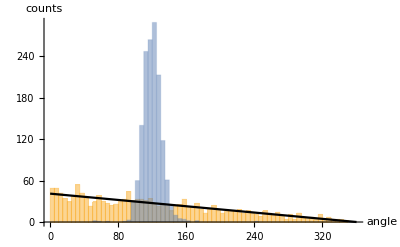

```mathematica
Show[Histogram[{
Flatten[randomAngles,1],
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}],
Plot[{Length@Flatten[angles3,1]/72*2(1-x/360)},{x,0,360},PlotStyle->Black]
]
```

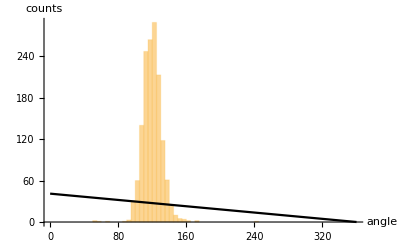

```mathematica
Show[Histogram[{
Flatten[angles3,1]
},{0,360,5},AxesLabel->{"angle","counts"}],
Plot[{Length@Flatten[angles3,1]/72*2(1-x/360)},{x,0,360},PlotStyle->Black]
]
```

### Fit result

```mathematica
Show[
imgColor,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices]]
]
```

## Vertices - Image 2

### Triple vertices

We define triple vertices as those branch points determined that are more than 10 pixels distant from other branch points (4-arm vertices are decomposed into two triple vertices in the network skeleton).

```mathematica
tripleVerticesRaw2=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@branchPointCoords2,0.]]}]/@branchPointCoords2,#[[-1]]>10&];
Length@tripleVerticesRaw2
```

347

So far, we got rid off 3-fold vertices that lie close by as we interpret those as 4-fold vertices that are decomposed in the skeleton network. However, there are also 4-fold vertices that remain as such in the skeleton network. We now identify those by counting the number of white pixels in the 3x3 neighborhood of a branch point. Triple vertices have 4 (one center + 3 arms), 4-fold vertices have 5 white pixels in this region .

```mathematica
tripleVertices2=Block[{
tvs=tripleVerticesRaw2,
branches=branchImPrun2,
verticesImg,
verticesMorph,
quadVerts
},
verticesImg=ImageMultiply[ImageReflect@Dilation[Image[Transpose@SparseArray[Thread[Round[(tvs[[All,1]]+0.5)]->1],{1000,1000}]],ConstantArray[1,{3,3}]],branches];
verticesMorph=MorphologicalComponents[verticesImg];
quadVerts=Keys@Select[ComponentMeasurements[verticesMorph,"Count"],Values[#]>4&];

If[Length[quadVerts]>0,
verticesMorph=Binarize@ColorNegate@Image@Clip[verticesMorph/.Thread[quadVerts->-1],{-1,0}];
quadVerts=ImageValuePositions[MorphologicalBranchPoints[verticesMorph],1];

Select[tvs,Min[Function[x,Norm[x-#[[1]]]]/@quadVerts]>0.1&],
tvs
]
];
```

```mathematica
Length@tripleVertices2
```

347

### 4-fold vertices

```mathematica
quadrupleVerticesRaw2=Complement[branchPointCoords2,tripleVertices2[[All,1]]];
quadrupleVertices2=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@quadrupleVerticesRaw2[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@quadrupleVerticesRaw2],I];
Length@quadrupleVertices2
```

10

```mathematica
vertices2=Join[tripleVertices2,quadrupleVertices2];
```

```mathematica
HighlightImage[branchIm2,{AbsolutePointSize[3],tripleVertices2,AbsolutePointSize[6],quadrupleVertices2}]
```

-Graphics-

## Analysis of triple vertices - Image 2

Experimental network data labeled by pixel positions

```mathematica
dataraw=ImageData[imgProj2[[1]]];
```

```mathematica
{dy,dx}=Dimensions@dataraw;
```

```mathematica
data=Table[{j-0.5,dy-i+0.5,dataraw[[i,j]]},{i,1,Dimensions[dataraw][[1]]},{j,1,Dimensions[dataraw][[2]]}];
```

### Analysis

The fit data for each vertex is taken as the data points within a 20 pixel large radius around the branch point. If a second branch point lies closer than 20 pixels, the radius is reduced to this distance.

```mathematica
vertex3Data=Table[{vertex[[1]],{#[[1]]-vertex[[1,1]],#[[2]]-vertex[[1,2]],#[[3]]}&/@Select[Flatten[data[[Max[1,Floor[dy-vertex[[1,2]]-25]];;Min[dy,Ceiling[dy-vertex[[1,2]]+25]],Max[1,Floor[vertex[[1,1]]-25]];;Min[dx,Ceiling[vertex[[1,1]]+25]]]],1],Norm[vertex[[1]]-#[[{1,2}]]]<Min[20,vertex[[2]]]&]},{vertex,tripleVertices2}];
```

```mathematica
Manipulate[
Show[
ListDensityPlot[vertex3Data[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Disk[{0,0},1]]
],{i,1,Length@vertex3Data}]
```

Fit triple vertices and exclude those for which the fit does not converge.

```mathematica
vertex3MeasurementsRaw2=ParallelTable[measureData[data,3],{data,vertex3Data},Method->"FinestGrained"];
```

FindMinimum::regex: Reached the point {16.1803,0.,-1.23319,0.05,0.65}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

FindMinimum::regex: Reached the point {16.1803,0.,0.05,0.65,-1.03319}, which is outside the region {{-10.,-10.,-6.28319,-6.28319,-6.28319},{10.,10.,6.28319,6.28319,6.28319}}.

```mathematica
fittedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],ListQ[#[[2]]]&][[All,1]];
failedVertices=Select[Transpose[{Range@Length@#,#}&@vertex3MeasurementsRaw2],#[[2]]==I&][[All,1]];
vertex3Measurements=DeleteCases[vertex3MeasurementsRaw2,I];
Length[vertex3Data]
Length[vertex3Measurements]
```

0

343

```mathematica
failedVertices
```

{64,204,268,298}

```mathematica
Show[
ListDensityPlot[vertex3Data[[#,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Annulus[{0,0},{20,40}]]
]&/@failedVertices
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[
Show[
ListDensityPlot[(vertex3Data[[fittedVertices]])[[Floor@i,2]],InterpolationOrder->0,PlotRange->All],
Graphics[Join[{Annulus[{0,0},{20,40}],
Disk[vertex3Measurements[[Floor@i,;;2]]-(tripleVertices[[fittedVertices]])[[Floor@i,1]],1]},
{Darker@Red,Thick},
Flatten[Function[p,Line[{{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]],{p[[1]],p[[2]]}-(tripleVertices[[fittedVertices]])[[Floor@i,1]]+20{Cos[#],Sin[#]}}]&/@p[[3;;]]]@vertex3Measurements[[Floor@i]],1]]]
],{i,1,Length@vertex3Measurements}]
```

```mathematica
angles32=(Join[#,{360-Total@#}]&@(180/Pi*Differences[#]))&/@(vertex3Measurements[[All,3;;]]);
```

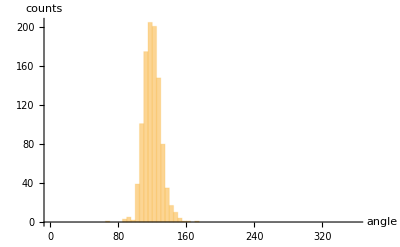

```mathematica
Histogram[{
Flatten[angles32,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[angles32,1]]
```

120.

```mathematica
StandardDeviation[Flatten[angles32,1]]
```

10.1823

#### FitList

```mathematica
vertex3MeasurementsRaw2
```

{{750.509,981.485,-3.03253,-0.833205,0.995274},{569.494,980.515,-1.68332,0.330036,2.44721},{223.474,978.506,-2.42905,-0.426922,1.65219},{825.51,978.495,-2.71769,-0.807137,1.49366},{913.495,977.492,-2.29927,-0.00744718,1.93241},{56.5125,976.493,-2.75239,-0.771245,1.24386},{943.512,975.503,-1.0032,0.973256,3.02884},{359.32,972.284,-2.38202,-0.346811,1.8704},{678.503,967.484,-2.47208,-0.338662,2.02284},{17.4923,966.505,-2.04724,0.109813,2.26058},{373.857,967.533,-1.24114,0.769467,2.88375},{280.516,960.479,-1.00704,1.2457,3.01348},{694.779,961.699,-1.11856,0.773984,2.78673},{145.486,959.487,-2.31118,-0.34985,1.93353},{778.491,954.5,-1.59709,0.484163,2.42666},{194.511,949.519,-1.10544,0.791703,2.95255},{615.503,946.493,-2.38047,-0.409499,1.82881},{956.563,945.552,-2.31649,-0.376311,1.87689},{845.496,945.498,-2.2257,-0.218642,1.90191},{561.521,942.487,-2.7759,-0.717797,1.22586},{87.5032,941.518,-1.92528,0.192507,2.20674},{888.512,941.493,-3.12167,-0.760161,0.992906},{293.486,940.51,-2.20008,0.198324,2.17649},{127.509,939.51,-1.20035,0.841388,2.97808},{633.745,939.69,-1.23796,0.896143,2.82912},{391.922,934.165,-1.92477,0.0361053,2.20845},{467.498,932.521,-1.21936,0.901938,2.97097},{413.516,931.519,-1.34579,0.478283,2.91275},{990.086,930.465,-1.50338,1.50912,2.66309},{281.529,925.501,-3.0804,-0.953801,0.931067},{580.491,924.504,-1.66696,0.455242,2.3516},{914.501,916.493,-1.89027,0.45379,2.3605},{784.501,914.498,-2.47276,-0.422114,1.84466},{682.357,907.555,-2.96885,-0.772286,1.30011},{647.491,905.492,-2.1592,-0.0488142,2.04109},{810.508,901.518,-0.991183,0.761976,2.63529},{475.546,892.832,-2.72868,-0.687491,1.53272},{701.485,888.503,-2.03217,0.134882,2.34869},{56.5137,884.515,-3.07378,-0.956933,0.931138},{579.493,883.506,-2.41755,-0.357864,1.72636},{748.568,883.243,-1.44334,0.720794,2.83858},{30.884,881.59,-1.80039,0.154176,2.26306},{288.498,877.498,-2.77745,-0.370858,1.55768},{372.135,876.766,-3.03473,-0.970265,1.20779},{620.514,867.508,-0.968305,0.81108,2.74783},{330.526,859.506,-1.29505,0.659706,2.67734},{842.505,857.477,-2.27264,-0.0782819,2.12545},{224.527,856.499,-2.5379,-0.6465,1.58501},{890.508,856.501,-2.99495,-0.829607,1.08029},{387.496,854.491,-2.20513,-0.00888092,2.17931},{140.516,852.49,-2.69038,-0.89637,1.32601},{423.521,850.511,-0.962803,0.848356,2.99711},{255.041,847.758,-3.0263,-1.00101,1.16165},{545.287,849.194,-1.04668,0.827837,2.95732},{77.8123,836.363,-2.6024,-0.541946,1.77382},{908.96,837.955,-1.77444,0.335671,2.38391},{974.19,839.054,-1.43207,0.589477,3.01153},{817.498,830.514,-2.77951,-0.951264,0.837683},{89.5447,829.532,-1.30207,0.653796,2.61434},{159.467,827.497,-2.45481,-0.0635197,2.18527},{34.4981,822.507,-2.23929,0.0740073,2.24061},{176.532,822.51,-1.10918,0.625294,2.80247},{751.506,815.496,-2.66467,-0.631179,1.4025},ⅈ,{568.502,807.502,-1.92604,0.254367,2.23534},{701.502,806.475,-2.33339,-0.0740241,1.88333},{774.501,799.488,-1.7368,0.630784,2.55416},{977.3,797.129,-2.49075,-0.592055,1.63486},{902.559,796.042,-2.68931,-0.617373,1.4763},{188.171,792.975,-2.51826,-0.245,1.90109},{676.499,791.514,-2.16115,0.21016,2.25505},{374.494,784.496,-1.8427,0.440545,2.25796},{560.275,775.83,-2.80388,-0.663705,1.37967},{625.484,775.492,-2.36474,-0.332805,1.76218},{97.4046,774.665,-2.4359,-0.494274,1.59812},{844.488,770.515,-1.66093,0.220083,2.05245},{942.517,769.508,-1.5136,0.666958,2.59007},{764.523,767.51,-0.938617,1.18605,2.99846},{367.52,765.486,-2.76412,-0.78704,1.20605},{655.509,765.523,-1.36998,0.795663,2.796},{507.534,764.693,-1.9539,0.158459,2.54061},{235.503,762.509,-1.63415,0.484093,2.37541},{77.4714,759.506,-2.00539,0.602917,2.39027},{146.039,754.384,-1.38081,0.797663,2.9576},{442.486,751.486,-2.37998,-0.452066,1.90757},{591.487,747.504,-2.03414,0.557515,2.34525},{316.505,745.502,-1.7077,0.467999,2.26084},{773.488,742.487,-2.31805,-0.358472,1.61553},{838.508,740.503,-3.02614,-0.762372,1.23543},{232.504,734.49,-2.79729,-0.912679,1.43741},{397.495,730.514,-2.04066,0.319428,2.2135},{927.987,728.255,-1.25198,0.972546,2.92559},{481.523,723.531,-0.996119,0.884184,3.07164},{63.5071,722.498,-3.04022,-0.809392,1.2292},{857.486,721.497,-1.79264,0.236929,2.33177},{578.791,711.004,-2.88441,-0.604239,1.3293},{386.531,711.484,-2.99688,-0.919563,1.02212},{258.494,707.502,-2.01362,-0.0678485,2.381},{938.491,706.492,-2.15211,-0.151076,2.12716},{154.496,703.479,-2.51051,-0.569133,1.74302},{741.525,699.497,-2.92505,-0.832185,0.981969},{852.776,697.772,-2.74468,-0.818127,1.42856},{190.241,690.801,-2.75691,-0.677644,1.21184},{505.353,689.936,-1.8608,0.365362,2.23529},{649.509,688.499,-0.770805,1.11369,3.08125},{179.319,686.694,-1.94369,0.413061,2.40982},{96.238,682.619,-1.95509,0.321378,2.2431},{245.08,674.705,-3.08093,-0.960487,1.192},{665.317,672.939,-1.85225,0.297322,2.21505},{89.5069,663.508,-2.56442,-0.699984,1.23992},{308.515,663.496,-2.79966,-0.801312,1.23187},{770.502,662.511,-1.90742,0.19956,2.25584},{802.509,662.526,-1.17423,0.778734,2.93896},{662.677,661.206,-2.69504,-0.72993,1.41563},{260.819,651.516,-2.0729,0.188513,2.17109},{611.488,646.511,-2.22028,0.179074,2.1083},{500.498,640.497,-2.44437,-0.381026,1.69826},{402.162,639.888,-2.85496,-0.776432,1.3629},{49.5012,634.51,-1.49605,0.575725,2.52494},{601.507,632.49,-2.94344,-0.904344,1.03564},{456.505,630.468,-2.94144,-0.485412,1.40076},{414.281,627.938,-1.95799,0.0991602,2.4084},{338.481,625.501,-2.06751,0.152072,2.22062},{154.841,620.745,-1.53003,1.00036,2.77501},{477.52,620.51,-1.3203,0.735223,2.77847},{742.509,614.488,-3.11024,-0.875657,0.995266},{553.514,613.507,-1.5893,0.598735,2.58364},{698.5,612.511,-2.19042,0.124999,2.20938},{974.513,612.507,-2.77704,-0.610066,1.1771},{330.508,611.499,-2.98868,-0.831861,1.03614},{52.4902,610.494,-2.39891,-0.570758,1.74035},{237.501,609.5,-2.9601,-0.836222,0.945857},{828.505,607.49,-2.5583,-0.43484,1.85246},{960.487,605.514,-2.03271,0.460232,2.32665},{156.333,600.32,-2.53247,-0.42657,1.63614},{846.603,598.868,-1.29723,0.693359,2.68709},{174.496,589.524,-1.54905,0.570066,2.53211},{765.475,587.505,-1.68693,0.337088,2.2971},{850.196,584.19,-2.39391,-0.380446,1.77848},{273.501,583.501,-1.37687,0.730771,2.74898},{399.092,575.521,-3.08278,-0.966151,1.04056},{357.498,572.506,-2.02385,0.107148,2.208},{86.4791,570.467,-2.33275,-0.45454,1.88336},{675.856,569.261,-3.07222,-0.89614,1.09598},{657.456,568.496,-2.10799,0.0522008,2.1977},{101.58,564.049,-1.43574,0.63302,2.83851},{408.457,562.491,-2.18667,-0.101908,2.1887},{552.505,559.501,-2.40537,-0.566987,1.47854},{29.2629,556.256,-2.35219,-0.283983,1.73633},{925.526,556.485,-2.88625,-0.925315,0.812517},{897.504,551.505,-2.16454,0.0893733,2.20078},{768.495,550.503,-2.48027,-0.558166,1.83545},{20.8264,548.749,-1.34635,0.664542,2.85634},{282.195,542.704,-2.33257,-0.3152,1.7556},{827.513,541.497,-3.05768,-0.828526,1.07547},{499.424,541.198,-1.92735,0.344473,2.27261},{802.511,535.527,-1.51644,0.349652,2.77581},{339.513,534.469,-3.07605,-0.800871,1.0245},{389.5,528.493,-3.01145,-0.906697,1.09485},{347.381,526.629,-2.07122,0.0454789,2.3588},{492.759,524.327,-3.01705,-0.968267,1.15596},{605.677,521.316,-1.5797,0.512742,2.47578},{457.481,519.504,-2.06807,0.132843,2.16745},{729.608,519.399,-1.71444,0.610519,2.50415},{107.498,518.477,-2.32314,-0.56997,1.60562},{23.5053,515.493,-2.57156,-0.598667,1.67243},{189.498,509.5,-2.63714,-0.649931,1.48573},{407.488,504.496,-2.10143,0.0351666,2.18679},{449.703,504.812,-1.13302,1.08547,3.121},{727.51,504.497,-2.67248,-0.795014,1.37376},{944.546,496.761,-2.82895,-0.659735,1.56723},{605.497,494.5,-2.64504,-0.652598,1.56531},{987.203,491.421,-2.83097,-0.602926,1.01835},{245.508,491.498,-2.88991,-0.882531,1.05449},{148.411,490.895,-1.64344,0.345608,2.50376},{64.1332,488.794,-1.69588,0.440267,2.55461},{219.5,484.501,-1.79705,0.253471,2.44663},{963.498,482.498,-1.79278,0.442073,2.50789},{680.523,471.506,-1.34818,0.665282,2.96468},{904.885,472.256,-1.00875,0.850474,2.89197},{557.195,470.83,-1.67111,0.29998,2.4689},{630.501,470.518,-1.33646,0.30803,2.24084},{338.084,466.113,-2.35806,-0.187553,1.87712},{750.501,465.499,-2.39349,-0.0301098,1.88451},{381.514,461.488,-3.11174,-0.872008,0.978612},{791.504,458.513,-1.18723,0.748865,2.85107},{212.473,455.53,-1.21057,1.31347,3.13231},{270.82,454.205,-2.20949,0.0868413,2.09375},{323.513,451.529,-1.23716,0.802092,2.86215},{913.523,449.504,-2.55934,-0.557055,1.72293},{448.507,447.505,-3.04143,-0.798649,1.06243},{554.556,446.972,-2.79396,-0.562791,1.47069},{950.504,445.503,-2.82798,-0.793738,1.12642},{400.552,437.66,-1.89202,0.130201,2.19709},{721.532,433.488,-3.05079,-0.903162,0.992225},{706.491,432.496,-1.99827,0.0940576,2.33541},{248.504,428.504,-2.92151,-0.951035,0.805765},{801.497,428.503,-2.35962,-0.346233,1.84597},{226.447,423.535,-2.20728,0.258822,2.20381},{392.503,419.49,-2.91936,-0.86446,1.0896},{492.49,418.51,-1.44767,0.817827,2.77109},{139.642,415.785,-2.38605,-0.314321,1.68782},{977.09,417.233,-1.85417,0.0615116,2.2998},ⅈ,{604.517,413.514,-1.08662,0.749133,2.74835},{342.493,409.488,-2.1507,0.0643772,2.18798},{778.513,404.512,-1.12358,0.838642,2.92618},{868.96,404.617,-3.0795,-1.21192,0.933124},{687.717,400.465,-3.08177,-1.20032,1.01777},{494.496,398.504,-2.53463,-0.557963,1.64764},{618.427,387.587,-1.90327,0.0245442,2.09385},{324.672,380.256,-3.02779,-0.866852,1.0622},{304.492,377.52,-2.0783,0.166663,2.19839},{949.524,377.516,-1.44798,0.557746,2.61448},{409.487,375.515,-1.95739,-0.156086,1.68955},{542.503,371.505,-1.99194,0.477984,2.80389},{449.227,365.587,-1.27671,0.633252,2.85874},{35.4897,363.501,-1.6142,0.262861,2.12488},{951.082,359.21,-2.56148,-0.35393,1.65464},{215.818,359.919,-1.28476,1.0554,3.13106},{788.516,357.49,-2.73386,-0.665277,1.53965},{603.502,356.515,-2.90594,-0.548076,0.970235},{882.5,355.491,-2.56146,-0.22083,1.78101},{119.011,346.454,-1.69714,0.350578,1.88494},{801.479,347.513,-1.66742,0.370765,2.50214},{935.519,347.522,-1.32434,0.667194,2.71927},{868.646,346.5,-1.42349,0.586807,2.91257},{370.513,338.504,-1.48716,0.559907,2.54842},{700.483,337.497,-2.48818,-0.38101,1.77654},{716.532,330.509,-1.334,0.561043,2.70764},{114.507,328.497,-2.66841,-0.604775,1.24222},{631.496,322.497,-2.36918,-0.601203,1.91873},{23.5037,317.502,-3.0704,-0.888503,1.11414},{232.497,316.487,-2.2447,-0.0642183,2.06371},{938.589,314.465,-2.49996,-0.613769,1.48651},{520.977,312.97,-2.69558,-0.618102,1.28341},{872.489,312.494,-2.46693,-0.476685,1.70438},{258.516,310.497,-0.989236,0.898308,2.78184},{597.48,310.482,-2.3207,-0.247125,1.9662},{663.524,309.529,-1.35174,0.657471,2.78943},{151.49,300.514,-2.03536,0.150263,2.38345},{212.507,297.495,-1.35491,0.644227,2.90585},{479.496,297.51,-1.9034,0.289188,2.22439},{915.5,297.502,-1.24769,0.629847,2.22863},{374.48,293.527,-2.09779,0.113905,2.22666},{816.316,292.781,-1.70173,0.327117,2.34238},{50.4879,287.5,-1.79214,0.347037,2.37216},{367.638,280.792,-3.02745,-0.996861,1.09484},{567.678,281.283,-1.40591,0.710242,2.7306},{813.107,276.441,-2.8817,-0.957185,1.29962},{471.508,272.494,-2.74756,-0.758471,1.26112},{727.506,270.503,-2.31684,-0.493917,1.72358},{45.5053,266.496,-2.76979,-0.776981,1.3658},{451.494,264.512,-1.91347,0.353802,2.36378},{931.474,262.507,-2.17377,0.0735312,2.17723},{981.499,259.493,-1.21333,0.711926,3.00779},{302.317,256.83,-1.82975,0.275196,2.33173},{673.346,257.004,-2.17845,-0.370276,1.7577},{761.494,248.506,-1.24109,0.632319,2.48724},{919.521,244.493,-3.12269,-0.903246,1.02044},{698.509,243.496,-1.85772,0.643318,2.53036},{568.525,241.488,-2.77565,-0.665333,1.41625},{227.491,239.482,-2.32354,-0.16705,1.96524},{295.522,238.482,-2.86656,-0.742558,1.15099},{441.096,235.665,-3.106,-0.987812,1.20667},{834.505,234.485,-2.32998,-0.0226834,2.02435},{400.504,232.507,-2.15054,0.131602,2.19821},ⅈ,{521.498,225.505,-1.94751,0.448393,2.32436},{588.306,225.033,-1.88012,0.35785,2.45344},{652.502,220.492,-2.94481,-0.833663,1.0798},{881.362,221.559,-1.29474,0.822375,2.85023},{117.361,219.469,-2.20464,-0.293911,2.13289},{205.955,217.612,-1.17825,0.774404,3.04509},{635.268,216.744,-1.84237,0.233448,2.4592},{777.495,214.496,-2.40898,-0.223708,2.08705},{687.505,213.508,-2.88138,-0.774618,1.14107},{985.192,211.077,-2.89198,-0.627169,1.27553},{803.506,204.512,-1.18113,0.736077,2.66171},{948.492,204.514,-2.01869,0.147273,2.23522},{155.508,203.512,-1.28683,0.639538,2.63689},{329.5,197.487,-1.93073,-0.017204,2.21281},{367.702,192.622,-1.52869,0.801544,2.80968},{889.504,190.501,-2.39452,-0.345734,1.80117},{938.512,187.487,-2.96369,-1.0167,1.0575},{219.193,185.059,-2.43999,-0.326454,1.96491},{461.498,183.49,-2.26958,-0.335453,1.84001},{716.505,182.516,-1.93025,0.335351,2.3292},{605.645,181.56,-1.74411,0.489951,2.35414},{502.509,174.502,-0.990808,0.96624,3.07823},{319.493,172.502,-2.99479,-0.646345,1.1801},{370.498,171.482,-2.52482,-0.471459,1.76213},{183.492,166.492,-1.85596,0.169301,2.66288},{816.81,159.802,-2.29928,-0.159292,1.73652},{72.4672,157.482,-2.5668,-0.956246,1.61644},{270.498,155.506,-1.78355,0.46966,2.48719},{341.486,154.484,-1.75768,0.453337,2.41476},ⅈ,{423.494,151.497,-1.81462,0.403302,2.26862},{849.507,151.509,-1.19093,0.730688,2.79877},{704.634,148.588,-3.12841,-0.981824,1.22978},{959.483,148.499,-2.3232,-0.160856,1.97983},{534.499,139.5,-2.21587,-0.432219,1.45153},{168.517,131.507,-3.04583,-0.934813,0.968166},{588.249,129.365,-3.12204,-0.928801,1.14633},{722.496,126.523,-1.99866,0.213506,2.31004},{781.512,125.521,-1.32177,0.758745,2.68895},{16.496,115.466,-2.24368,0.0939657,1.95869},{130.516,111.506,-3.05378,-0.953896,0.832623},{602.492,111.496,-2.05583,-0.00551468,2.23282},{640.232,112.203,-3.09413,-1.0735,0.956135},{110.495,110.485,-2.07103,-0.0104149,2.2363},{866.497,109.499,-2.24043,-0.248347,2.02502},{934.815,109.257,-2.93695,-0.944412,1.16732},{339.497,105.484,-2.37081,-0.475398,1.82559},{421.473,105.466,-2.29477,-0.0917386,1.93092},{186.491,104.481,-2.20586,-0.0892079,2.13886},{488.504,99.5075,-1.26401,0.774903,2.83628},{898.498,95.5107,-1.59176,0.494112,2.5005},{411.519,94.514,-2.96524,-0.950374,0.857961},{248.943,92.1947,-0.920671,1.1746,3.07968},{384.177,85.7236,-1.8763,0.41843,2.51867},{154.492,81.5076,-1.77349,0.473554,2.33336},{791.491,79.5004,-2.47333,-0.363397,1.70629},{712.788,75.2168,-2.84538,-0.728115,1.4854},{261.488,69.4887,-2.05922,-0.0800198,1.93669},{594.493,69.4992,-2.42881,-0.491705,1.69078},{979.493,68.5075,-1.64508,0.367203,2.5486},{658.492,67.4868,-2.32565,-0.129811,1.95975},{308.505,65.4968,-1.01789,0.999876,3.04799},{830.509,65.5266,-1.42068,0.838728,2.79723},{494.495,57.4998,-2.66341,-0.390381,1.56795},{645.761,53.7722,-1.28377,0.84002,2.99118},{92.4747,51.4829,-2.46994,-0.396835,1.62446},{138.514,45.4759,-2.89559,-0.894817,0.911252},{747.487,44.5013,-1.66489,0.532623,2.49323},{445.5,41.5072,-2.00256,0.300244,2.2013},{324.48,40.4896,-2.15093,-0.00936143,2.19891},{361.5,38.5147,-1.20945,0.902389,3.033},{248.508,32.4998,-2.57069,-0.628572,1.2344},{567.505,31.4943,-2.79773,-0.76719,1.11364},{911.481,30.4658,-2.25181,-0.181323,2.04935},{961.519,26.495,-3.01728,-0.933022,0.952911},{746.161,23.3153,-2.56438,-0.553752,1.58045},{549.493,23.5114,-1.85848,0.445218,2.43565},{734.516,15.5185,-1.71333,0.626385,2.57935},{845.354,13.9434,-2.5077,-0.016887,1.91092}}

### Fit result

```mathematica
Show[
imgColor2,
Graphics[Join[{RGBColor[{255,255,255}/255],Thick},Flatten[Function[p,Line[{{p[[1]],p[[2]]},{p[[1]],p[[2]]}+15{Cos[#],Sin[#]}}]&/@p[[3;;]]]/@vertex3Measurements,1],
{RGBColor[{0,0,0}/255],Thick},Circle[#,10]&/@quadrupleVertices2]]
]
```

## Combined

```mathematica
anglesComb=Join[angles3,angles32];
```

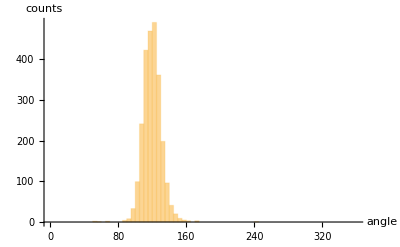

```mathematica
Histogram[{
Flatten[anglesComb,1]
},{0,360,5},AxesLabel->{"angle","counts"}]
```

```mathematica
Mean[Flatten[anglesComb,1]]
StandardDeviation[Flatten[anglesComb,1]]
```

120.

10.9308

## Domain statistics

## Image 1

Determine the domains alone:

```mathematica
domainIm=Pruning[Pruning@branchImPrun,Infinity]
```

-Graphics-

```mathematica
domains=MorphologicalComponents[ColorNegate@domainIm,"CornerNeighbors"->False];
```

```mathematica
domains//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas=SortBy[ComponentMeasurements[domains,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds=Keys@domainMeas;
```

```mathematica
Max[dx^2Values[domainMeas][[All,1]]]
```

349.233

```mathematica
Max[dx^2Values[domainMeas][[All,1]]]
```

349.233

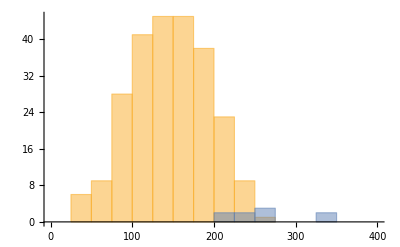

```mathematica
Histogram[{dx^2Select[Values@domainMeas,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas,#[[2]]>=1&][[All,1]]},{0,400,25}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds}],#>0&];,b]
```

```mathematica
Max[cornerNumber]
```

9

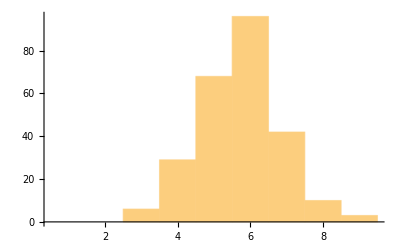

```mathematica
Histogram[cornerNumber,{0.5,10,1}]
```

```mathematica
N@Mean[cornerNumber]
```

5.7126

```mathematica
N@StandardDeviation[cornerNumber]
```

1.13517

## Image 2

Determine the domains alone:

```mathematica
domainIm2=Pruning[Pruning@branchImPrun2,Infinity];
```

```mathematica
domains2=MorphologicalComponents[ColorNegate@domainIm2,"CornerNeighbors"->False];
```

```mathematica
domains2//Colorize
```

-Graphics-

### Analyze domain-size and hole correlation

Length unit per pixel [µm]

```mathematica
dx=0.2125481;
```

```mathematica
domainMeas2=SortBy[ComponentMeasurements[domains2,{"Area","Holes"}],Values[#][[1]]&][[;;-2]];
```

```mathematica
domainInds2=Keys@domainMeas2;
```

```mathematica
Max[dx^2Values[domainMeas2][[All,1]]]
```

538.416

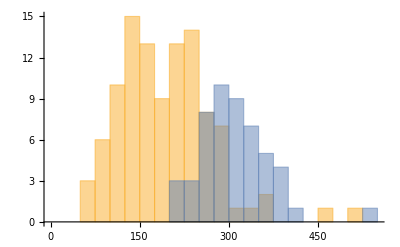

```mathematica
Histogram[{dx^2Select[Values@domainMeas2,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeas2,#[[2]]>=1&][[All,1]]},{0,550,25}]
```

### Number of corners of each domain

Have to take care of 4-fold vertices. In the branch network they fall apart into two triple vertices close by.
For some bubbles count two corners although above we would have classified it as a single 4-fold vertex.

```mathematica
Monitor[cornerNumber2=Select[Table[Block[{
mask=Dilation[Image[Map[If[#==b,1,0]&,domains2,{2}]],DiskMatrix[1]],
cornerCoords,
corners3,
corners4Raw,
corners4
},
cornerCoords=ImageValuePositions[ImageMultiply[branchPoints2,mask],1];
corners3=Select[Function[x,{x,Min[DeleteCases[Norm[x-#]&/@cornerCoords,0.]]}]/@cornerCoords,#[[-1]]>10&];
corners4Raw=Complement[cornerCoords,corners3[[All,1]]];
corners4=DeleteCases[Function[x,If[Min[DeleteCases[Norm[x[[2]]-#]&/@corners4Raw[[;;x[[1]]]],0.]]>10,x[[2]],I]]/@Transpose[{Range[Length[#]],#}&@corners4Raw],I];
Length[corners3]+Length[corners4]
],
{b,domainInds2}],#>0&];,b]
```

```mathematica
Max[cornerNumber2]
```

10

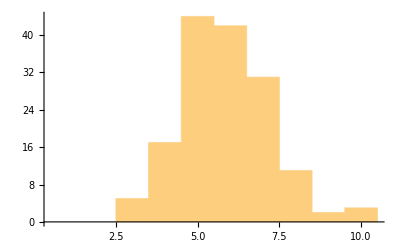

```mathematica
Histogram[cornerNumber2,{0.5,11,1}]
```

```mathematica
N@Mean[cornerNumber2]
```

5.85806

```mathematica
N@StandardDeviation[cornerNumber2]
```

1.38376

## Combined

```mathematica
domainMeasComb=Join[domainMeas,domainMeas2];
cornerNumberComb=Join[cornerNumber,cornerNumber2];
```

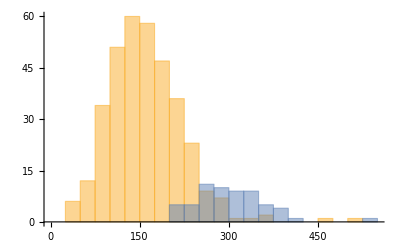

```mathematica
Histogram[{dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]},{0,550,25}]
```

```mathematica
Mean/@{dx^2Values[domainMeasComb][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]==0&][[All,1]],dx^2Select[Values@domainMeasComb,#[[2]]>=1&][[All,1]]}
```

{181.011,160.202,302.049}

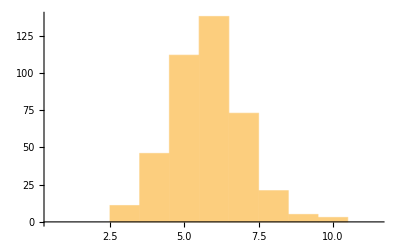

```mathematica
Histogram[cornerNumberComb,{0.5,12,1}]
```

```mathematica
N@Mean[cornerNumberComb]
N@StandardDeviation[cornerNumberComb]
```

5.76773

1.23564